```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/eric/git/QEA/Module 2/boat1-Matrix math

### Breathing rectangle

```mathematica
rectangle1={{1, -1, -1, 1}, {2, 2, -2, -2}};
Animate[
scaleFactor:=1-Abs[Sin[θ]]^5.5;
scaleMatrix:={{scaleFactor, 0}, {0, scaleFactor}};
rotationMatrix:=({{Cos[θ], -Sin[θ]}, {Sin@θ, Cos@θ}});
data=rotationMatrix.scaleMatrix.rectangle1;
(* Transposing the matrix converts {{Subscript[x, 1], Subscript[x, 2], ...},{Subscript[y, 1], y_(2,)...}}->{{Subscript[x, 1], Subscript[y, 1]},{Subscript[x, 2], Subscript[y, 2]}, ...} *)
Graphics[Polygon[Transpose@data],Axes->True,PlotRange->{6{-1,1},3{-1,1}}],{θ,-Pi,Pi}]
```

```mathematica
data[[1;;2]]
```

Dot::dotsh: Tensors {{-0.702223,-0.711957,2.},{0.711957,-0.702223,3.},{0.,0.,1.}} and {{0.869027,0.},{0.,0.869027}} have incompatible shapes.

{{-0.702223,-0.711957,2.},{0.711957,-0.702223,3.},{0.,0.,1.}}.{{0.869027,0.},{0.,0.869027}}

```mathematica
data
```

{{-0.750168,-0.661247,2.},{0.661247,-0.750168,3.},{0.,0.,1.}}.{{0.869027,0.},{0.,0.869027}}.{{1,-1,-1,1},{2,2,-2,-2},{1,1,1,1}}

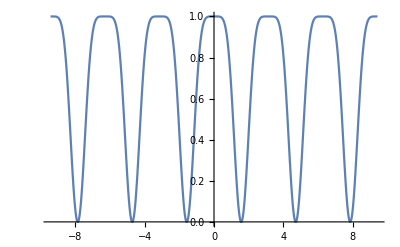

```mathematica
Plot[(1-Sin[θ]^6),{θ,-3Pi,3Pi}]
```

### Misc work

```mathematica
NSolve[Cos[θ]==Sin[θ],θ]
```

{{θ→ConditionalExpression[1. (-2.35619+6.28319 C[1]),C[1]∈Integers]},{θ→ConditionalExpression[1. (0.785398+6.28319 C[1]),C[1]∈Integers]}}

```mathematica
Inverse[{{1, -1}, {-1, 1}}]
```

Inverse::sing: Matrix {{1,-1},{-1,1}} is singular.

Inverse[{{1,-1},{-1,1}}]

```mathematica
rotationMatrix.{0,1}
```

{-1.22465×10^-16,-1.}

```mathematica
Clear[θ]
```

```mathematica
rotationMatrix
```

{{-1.,-1.22465×10^-16},{-1.22465×10^-16,-1.}}

```mathematica
{{Cos[θ], -Sin[θ]}, {-Sin@θ, Cos@θ}}.{0,-1}
```

{Sin[θ],-Cos[θ]}

```mathematica
{{Cos[θ], -Sin[θ]}, {-Sin@θ, Cos@θ}}.{0,-1}
```

{Sin[θ],-Cos[θ]}

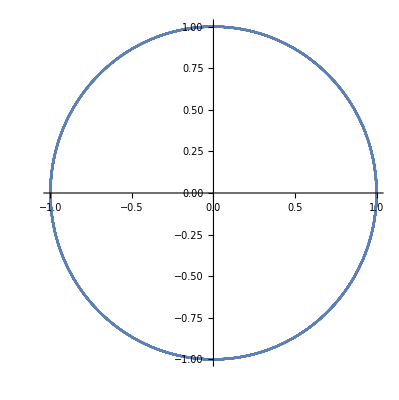

```mathematica
ParametricPlot[{Cos[θ],-Sin[θ]},{θ,-26.389378290154262,26.389378290154262}]
```

```mathematica
ParametricPlot[{Cos[θ],-Sin[θ]},{θ,-26.389378290154262,26.389378290154262}]
```

-Graphics-

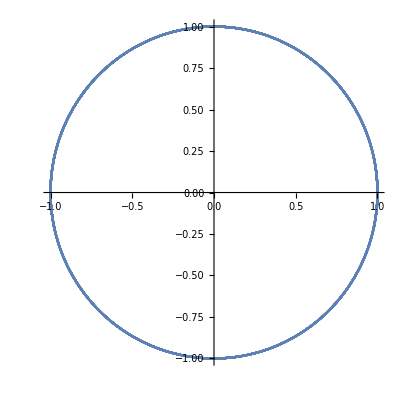

```mathematica
ParametricPlot[{-Sin[θ],Cos[θ]},{θ,-26.389378290154262,26.389378290154262}]
```

```mathematica
Inverse@scalingMatrix
```

{{1/2,0},{0,3}}

## Translation

### Symbolic Analysis

```mathematica
MatrixForm[({{1, 0, Subscript[t, x]}, {0, 1, Subscript[t, y]}, {0, 0, 1}}).({{x}, {y}, {1}})]
```

(x+t_x
y+t_y
1)

### Application

```mathematica
(* The extra row of 1's is necessary for the translation. This is actually a pentagon. *)
rectangle=({{1, -1, -1, 1, 3}, {2, 2, -2, -2, 0}, {1, 1, 1, 1, 1}});

Animate[
scaleFactor:=1-Abs[Sin[θ]]^5.5;
scaleMatrix:=({{scaleFactor, 0, 0}, {0, scaleFactor, 0}, {0, 0, 1}});
rotationMatrix:=({{Cos[θ], -Sin[θ], 0}, {Sin@θ, Cos@θ, 0}, {0, 0, 1}});
translationMatrix:=({{1, 0, 2}, {0, 1, 3}, {0, 0, 1}});
(* Notice that the tranformation matrices are multiplied first to improve efficiency for large shapes *)
data=(translationMatrix.rotationMatrix.scaleMatrix).rectangle;
(* Transposing the matrix converts {{Subscript[x, 1], Subscript[x, 2], ...},{Subscript[y, 1], y_(2,)...}}->{{Subscript[x, 1], Subscript[y, 1]},{Subscript[x, 2], Subscript[y, 2]}, ...} *)
Graphics[Polygon[Transpose@data[[1;;2,All]]],Axes->True,PlotRange->{6{-1,1},6{-1,1}}],{θ,-Pi,Pi}]
```

```mathematica
myfunction[x_]:=Module[{localvar},
localvar=6;
globalvar=10;
Return[5];
While[]

]
```

```mathematica
myfunction[6]
```

5

```mathematica
thing[Plot[1+1]]:=9
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

```mathematica
thing[Plot[1+1]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

9

```mathematica
Import["Transformer.jpg"]
```

-Graphics-

```mathematica
<<"import.wl"
```

hello world

```mathematica
f[5]
```

7